```mathematica
Clear["Global`*"]
DiiffScheme[f_,v1_,u0_,l1_,l2_,T_,h_,tau_]:=Module[{n1,n2,sm,vrs,sol,Ly1,Ly2,mtr,b,y},
n1=l1/h;
n2=l2/h;
sm=T/tau;
y[1,i_,j_]:=u0[(i-1) h,(j-1) h];
y[s_,1|(n1+1),j_]:=0;
y[s_,i_,1|(n2+1)]:=0;

Ly1[s_,i_,j_]:=(y[s,i+1,j]-2*y[s,i,j]+y[s,i-1,j])/h^2;
Ly2[s_,i_,j_]:=(y[s,i,j+1]-2*y[s,i,j]+y[s,i,j-1])/h^2;
mtr=Flatten[Table[
(y[s+1,i,j]-y[s,i,j])/tau==Ly1[s+1,i,j]+Ly2[s+1,i,j]+f[tau*(s+1),h*i,h*j],
{s,1,sm},{i,2,n1},{j,2,n2}]];

vrs=Flatten[Table[y[s+1,i,j],{s,1,sm},{i,2,n1},{j,2,n2}]];
sol=NSolve[mtr,vrs];
Do[y[s+1,i,j]=y[s+1,i,j]/. sol[[1]],{s,1,sm},{i,2,n1+1},{j,2,n2+1}];
Return[y]]

DiiffScheme2[f_,v1_,u0_,l1_,l2_,T_,h_,tau_]:=Module[{n1,n2,sm,vrs,sol,Ly1,Ly2,mtr,b,y, vrs2,mtr2,sol2},
n1=l1/h;
n2=l2/h;
sm=T/tau;
y[1,i_,j_]:=u0[(i-1) h,(j-1) h];
y[s_,1|(n1+1),j_]:=0;
y[s_,i_,1|(n2+1)]:=0;

Ly1[s_,i_,j_]:=(y[s,i+1,j]-2*y[s,i,j]+y[s,i-1,j])/h^2;
Ly2[s_,i_,j_]:=(y[s,i,j+1]-2*y[s,i,j]+y[s,i,j-1])/h^2;
Do[
mtr=Flatten[Table[
(y[s+1/2,i,j]-y[s,i,j])/tau==
Ly1[s+1/2,i,j]+
f[tau*(s-1),h*i,h*j]/2,

{i,2,n1},{j,2,n2}]];

vrs=Flatten[Table[y[s+1/2,i,j],{i,2,n1},{j,2,n2}]];
sol=NSolve[mtr,vrs];
Do[y[s+1/2,i,j]=y[s+1/2,i,j]/. sol[[1]],{i,2,n1+1},{j,2,n2+1}];

mtr2=Flatten[Table[
(y[s+1,i,j]-y[s+1/2,i,j])/tau==
Ly2[s+1,i,j]+
f[tau*(s-1),h*i,h*j]/2,

{i,2,n1},{j,2,n2}]];

vrs2=Flatten[Table[y[s+1,i,j],{i,2,n1},{j,2,n2}]];
sol2=NSolve[mtr2,vrs2];
Do[y[s+1,i,j]=y[s+1,i,j]/. sol2[[1]],{i,2,n1+1},{j,2,n2+1}],
{s,1,sm+1,1}
];
Return[y]]
```

```mathematica
f[t_,x_,y_]:=0;
l1=1;
l2=1;
v1[x_,y_]=0;
T=0.1;
tau=0.01;
h=0.1;
u0[x_,y_]:=Sin[(Pi*x)/l1]*Sin[(Pi*y)/l2];
Uex[t_,x_,y_]:=Exp[-((Pi/l1)^2+(Pi/l2)^2)t]*Sin[(Pi*x)/l1]*Sin[(Pi*y)/l2];
xlist=Table[i*h,{i,0,l1/h,1}];
ylist=Table[i*h,{i,0,l2/h,1}];
us=DiiffScheme[f,v1,u0,l1,l2,T,h,tau];
us2=DiiffScheme2[f,v1,u0,l1,l2,T,h,tau];
```

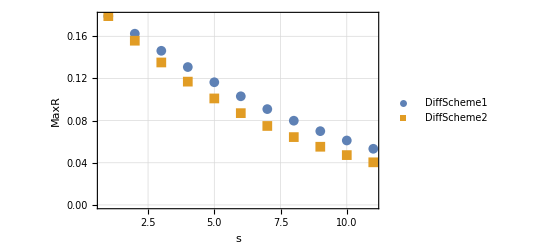

```mathematica
ds1={};
ds2={};
Do[
solE=Flatten[Table[Abs[us[s,i,j]-Uex[s*tau,xlist[[i]],ylist[[j]]]],{i,1,Length[xlist],1},{j,1,Length[ylist],1}],1];
solE2=Flatten[Table[Abs[us2[s,i,j]-Uex[s*tau,xlist[[i]],ylist[[j]]]],{i,1,Length[xlist],1},{j,1,Length[ylist],1}],1];
AppendTo[ds1,{s,Max[solE]}];
AppendTo[ds2,{s,Max[solE2]}],
{s,1,T/tau+1}];
ListPlot[{ds1,ds2},PlotMarkers->{{Automatic,10},{Automatic,10}},FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["s",16,Black,FontFamily->"Cambria"],Style["MaxR",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All,
PlotLegends->Placed[{Style["DiffScheme1",16,Black,FontFamily->"Cambria"],Style["DiffScheme2",16,Black,FontFamily->"Cambria"]},Right]]
```

```mathematica
Manipulate[
sol=Flatten[Table[{xlist[[i]],ylist[[j]],us[Round[t/tau+1],i,j]},{i,1,Length[xlist],1},{j,1,Length[ylist],1}],1];
sol2=Flatten[Table[{xlist[[i]],ylist[[j]],us2[Round[t/tau+1],i,j]},{i,1,Length[xlist],1},{j,1,Length[ylist],1}],1];
Column[{
Row[{
Plot3D[Uex[t,x,y],{x,0,l1},{y,0,l2},PlotRange->{{0,l1},{0,l2},{0,1}},AxesLabel->{"x","y","U"},ImageSize->320],
ListPlot3D[sol,PlotRange->{{0,l1},{0,l2},{0,1}},AxesLabel->{"x","y","U"},ImageSize->320],
ListPlot3D[sol2,PlotRange->{{0,l1},{0,l2},{0,1}},AxesLabel->{"x","y","U"},ImageSize->320]
}]
}],

{t,0,T,tau}]
```

```mathematica
dst1={};
dst2={};
Do[
AppendTo[dst1,{i,Timing[DiiffScheme[f,v1,u0,l1,l2,T,h,tau]][[1]]}];
AppendTo[dst2,{i,Timing[DiiffScheme2[f,v1,u0,l1,l2,T,h,tau]][[1]]}],
{i,1,100}]
```

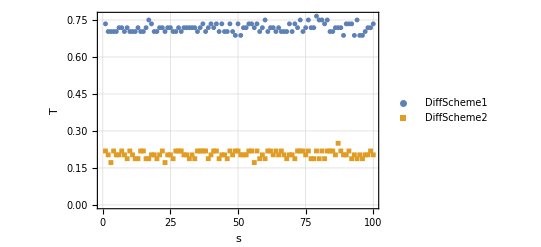

```mathematica
ListPlot[{dst1,dst2},PlotMarkers->{{Automatic,5},{Automatic,5}},FrameStyle->Directive[Black,12],PlotRange->All,Frame->True,FrameLabel->{Style["s",16,Black,FontFamily->"Cambria"],Style["T",16,Black,FontFamily->"Cambria"]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All,
PlotLegends->Placed[{Style["DiffScheme1",16,Black,FontFamily->"Cambria"],Style["DiffScheme2",16,Black,FontFamily->"Cambria"]},Right]]
```